## General Function Board

### Ecological model - Steady states

```mathematica
dSCdt=IS-VmD SC Z/(KmD+SC)-eC SC;
dDCdt=VmD SC Z/(KmD+SC)-VmU DC M/(KmU+DC)-eD DC+dZ Z+dM M;
dMdt=γM (1-φ)VmU DC M/(KmU+DC)-dM M;
dZdt=γZ φ VmU DC M/(KmU+DC)-dZ Z;
coex=Solve[{dMdt==0,dZdt==0,dSCdt==0,dDCdt==0},{M,Z,SC,DC}]//MatrixForm
SCeq1=SC/.coex[[1,1]];
DCeq1=DC/.coex[[1,1]];
Meq1=M/.coex[[1,1]];
Zeq1=Z/.coex[[1,1]];
SCeq2=SC/.coex[[1,2]];
DCeq2=DC/.coex[[1,2]];
Meq2=M/.coex[[1,2]];
Zeq2=Z/.coex[[1,2]];
SCeq3=SC/.coex[[1,3]];
DCeq3=DC/.coex[[1,3]];
Meq3=M/.coex[[1,3]];
Zeq3=Z/.coex[[1,3]];
```

(M→0 | Z→0 | SC→IS/eC | DC→0
M→(dM IS γM+dM eD KmU γM-IS VmU γM^2-dM IS γM φ-dM eD KmU γM φ+2 IS VmU γM^2 φ-IS VmU γM^2 φ^2-(dM eC γM (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(eC VmU γM^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(dM eC γM φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))-(eC VmU γM^2 φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(eC VmU γM^2 φ^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)))/(dM^2-dM^2 γM-dM VmU γM+dM VmU γM^2+dM^2 γM φ+dM VmU γM φ-2 dM VmU γM^2 φ-dM^2 γZ φ+dM VmU γM γZ φ+dM VmU γM^2 φ^2-dM VmU γM γZ φ^2) | Z→(-dM IS γZ φ-dM eD KmU γZ φ+IS VmU γM γZ φ-IS VmU γM γZ φ^2+(dM eC γZ φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))-(eC VmU γM γZ φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(eC VmU γM γZ φ^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)))/(-dM dZ+dM dZ γM+dZ VmU γM-dZ VmU γM^2-dM dZ γM φ-dZ VmU γM φ+2 dZ VmU γM^2 φ+dM dZ γZ φ-dZ VmU γM γZ φ-dZ VmU γM^2 φ^2+dZ VmU γM γZ φ^2) | SC→(-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)) | DC→-(dM KmU)/(dM-VmU γM+VmU γM φ)
M→(dM IS γM+dM eD KmU γM-IS VmU γM^2-dM IS γM φ-dM eD KmU γM φ+2 IS VmU γM^2 φ-IS VmU γM^2 φ^2-(dM eC γM (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(eC VmU γM^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(dM eC γM φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))-(eC VmU γM^2 φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(eC VmU γM^2 φ^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)))/(dM^2-dM^2 γM-dM VmU γM+dM VmU γM^2+dM^2 γM φ+dM VmU γM φ-2 dM VmU γM^2 φ-dM^2 γZ φ+dM VmU γM γZ φ+dM VmU γM^2 φ^2-dM VmU γM γZ φ^2) | Z→(-dM IS γZ φ-dM eD KmU γZ φ+IS VmU γM γZ φ-IS VmU γM γZ φ^2+(dM eC γZ φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))-(eC VmU γM γZ φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(eC VmU γM γZ φ^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)))/(-dM dZ+dM dZ γM+dZ VmU γM-dZ VmU γM^2-dM dZ γM φ-dZ VmU γM φ+2 dZ VmU γM^2 φ+dM dZ γZ φ-dZ VmU γM γZ φ-dZ VmU γM^2 φ^2+dZ VmU γM γZ φ^2) | SC→(-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)) | DC→-(dM KmU)/(dM-VmU γM+VmU γM φ))

### Steady state stability - Jacobian matrix

```mathematica
J=Simplify[{{D[dSCdt,SC],D[dSCdt,DC],D[dSCdt,M],D[dSCdt,Z]},{D[dDCdt,SC],D[dDCdt,DC],D[dDCdt,M],D[dDCdt,Z]},{D[dMdt,SC],D[dMdt,DC],D[dMdt,M],D[dMdt,Z]},{D[dZdt,SC],D[dZdt,DC],D[dZdt,M],D[dZdt,Z]}}];
JA=J/.M->Meq1/.Z->Zeq1/.SC->SCeq1/.DC->DCeq1; 
JB=J/.M->Meq2/.Z->Zeq2/.SC->SCeq2/.DC->DCeq2; 
JC=J/.M->Meq3/.Z->Zeq3/.SC->SCeq3/.DC->DCeq3; 
lambdaI={{λ,0,0,0},{0,λ,0,0},{0,0,λ,0},{0,0,0,λ}};
DC=Det[JC-lambdaI];
A1C=D[D[D[DC,λ],λ],λ]/6/.λ->0;
A2C=D[D[DC,λ],λ]/2/.λ->0;
A3C=D[DC,λ]/.λ->0;
A4C=DC/.λ->0;
COND1=A1C;
COND2=A3C;
COND3=A4C;
COND4=A1C A2C A3C-A3C^2-A1C^2 A4C;
```

### Parameter sensitivity

```mathematica
SA=Abs[Log[Abs[HO]]-Log[Abs[LO]]]/Abs[Log[Abs[HP]]-Log[Abs[LP]]];
```

### Temperature dependence - Baseline scenario

```mathematica
VmDx=VmD0 Exp[-EvD/(R(x+273))];
KmDx=KmD0 Exp[-EkD/(R(x+273))];
VmUx=VmU0 Exp[-EvU/(R(x+273))];
KmUx=KmU0 Exp[-EkU/(R(x+273))];
SC3ecox=SCeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx;
DC3ecox=DCeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx;
M3ecox=Meq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx;
Z3ecox=Zeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx;
φx=1-dM/(VmUx γM)-1/c;
SC3ecoevox=SC3ecox/.φ->φx;
DC3ecoevox=DC3ecox/.φ->φx;
M3ecoevox=M3ecox/.φ->φx;
Z3ecoevox=Z3ecox/.φ->φx;
```

```mathematica
φT0=φx/.x->x0;
SC3ecoφT0=SC3ecox/.φ->φT0;
SC3T0=SC3ecoevox/.x->x0/.φx->φT0;
ΔSCeco=SC3ecoφT0-SC3T0;
ΔSCecoevo=SC3ecoevox-SC3T0;
```

```mathematica
M3ecoφT0=M3ecox/.φ->φT0;
M3T0=M3ecoevox/.x->x0/.φx->φT0;
ΔMeco=M3ecoφT0-M3T0;
ΔMecoevo=M3ecoevox-M3T0;
```

```mathematica
Z3ecoφT0=Z3ecox/.φ->φT0;
Z3T0=Z3ecoevox/.x->x0/.φx->φT0;
ΔZeco=Z3ecoφT0-Z3T0;
ΔZecoevo=Z3ecoevox-Z3T0;
```

```mathematica
DC3ecoφT0=DC3ecox/.φ->φT0;
DC3T0=DC3ecoevox/.x->x0/.φx->φT0;
ΔDCeco=DC3ecoφT0-DC3T0;
ΔDCecoevo=DC3ecoevox-DC3T0;
```

```mathematica
ΔCtoteco=ΔSCeco+ΔMeco+ΔZeco+ΔDCeco;
ΔCtotecoevo=ΔSCecoevo+ΔMecoevo+ΔZecoevo+ΔDCecoevo;
```

## Figure 1b

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
COND1xφ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND2xφ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND3xφ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND4xφ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
M3ecoxφ=M3ecox/.dM->dMx/.testparam;
```

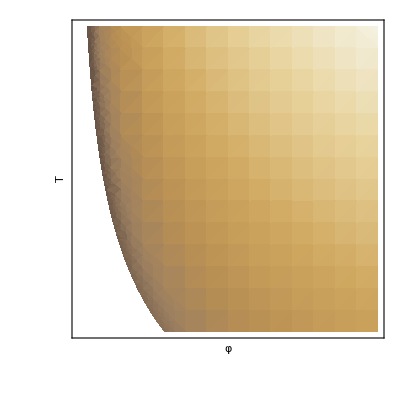

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min]
LogScaleLegend[min_,max_,colorfunction_,height_: 400]:=Module[{bareTicksList,numberedTicks,m,M,ml,Ml,minInArbitraryScale,maxInArbitraryScale,linearScaling},bareTicksList=First[Ticks/.AbsoluteOptions[LogLogPlot[x,{x,min,max}]]];
numberedTicks=(Select[bareTicksList/.{Superscript->Power},NumberQ[#[[2]]]&])[[All,{1,2}]];
m=Min[numberedTicks[[All,2]]];
M=Max[numberedTicks[[All,2]]];
ml=Min[numberedTicks[[All,1]]];
Ml=Max[numberedTicks[[All,1]]];
{minInArbitraryScale,maxInArbitraryScale}=ml+(Ml-ml) Log[{min,max}/m]/Log[M/m];
linearScaling[x_]:=(x-minInArbitraryScale)/(maxInArbitraryScale-minInArbitraryScale);
DensityPlot[y,{x,0,0.04},{y,0,1},AspectRatio->Automatic,PlotRangePadding->0,ImageSize->{Automatic,height},ColorFunction->colorfunction,FrameTicks->{{None,Select[Table[{linearScaling[r[[1]]],r[[2]]/.{Superscript[10.,n_]->Superscript[10,n]},{0,If[r[[2]]==="",0.15,0.3]},{If[r[[2]]==="",Thickness[0.03],Thickness[0.06]]}},{r,bareTicksList}],(#[[1]] (1-#[[1]])≥0&)]},{None,None}}]]
plotter[min_,max_,NumberOfTicks_]:=DensityPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},AxesLabel->{"φ","T"},
RegionFunction->Function[{φ,x,z},Evaluate[Im[M3ecoxφ]==0&&M3ecoxφ>0&&COND1xφ>0&&COND2xφ>0&&COND3xφ>0&&COND4xφ>0]],
PlotRange->Full,ColorFunctionScaling->False,FrameTicks->None,ColorFunction->(ColorData["CoffeeTones"][LogarithmicScaling[#,min,max]]&),
PlotLegends->LogScaleLegend[min,max,ColorData["CoffeeTones"],350,LegendLabel->"C"]]
plotter[600,10,5]
```

## Figure 1c

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
COND1paramT0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0/.testparam;
COND2paramT0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0/.testparam;
COND3paramT0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0/.testparam;
COND4paramT0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0/.testparam;
M3ecoparamT0=M3ecox/.dM->dMx/.x->T0/.testparam;
COND1paramT1=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0+5/.testparam;
COND2paramT1=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0+5/.testparam;
COND3paramT1=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0+5/.testparam;
COND4paramT1=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0+5/.testparam;
M3ecoparamT1=M3ecox/.dM->dMx/.x->T0+5/.testparam;
```

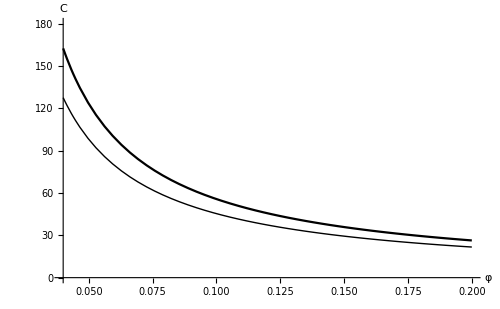

```mathematica
Plot1a=Plot[SC3ecox/.dM->dMx/.x->T0+5/.testparam,{φ,0.04,0.2},PlotRange->{{0.04,0.2},{0,180}},AxesOrigin->{0.04,0},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamT1]==0&&M3ecoparamT1>0&&COND1paramT1>0&&COND2paramT1>0&&COND3paramT1>0&&COND4paramT1>0]],
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","C"}];
Plot1b=Plot[SC3ecox/.dM->dMx/.x->T0/.testparam,{φ,0.04,0.2},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamT0]==0&&M3ecoparamT0>0&&COND1paramT0>0&&COND2paramT0>0&&COND3paramT0>0&&COND4paramT0>0]],
PlotStyle->{{Black}}];
Show[Plot1a,Plot1b]
```

## Figure 2 (a-d)

### Figure 2a

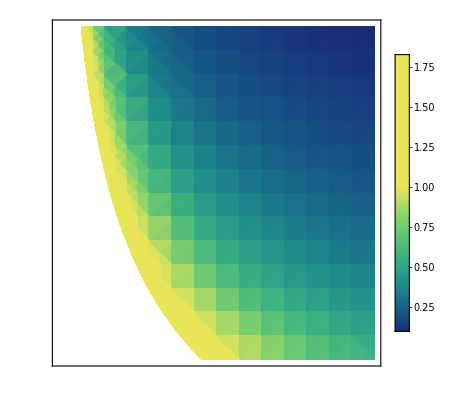

```mathematica
testT0c0={eC->10^-6,eD->10^-2,dMref->2 10^-4,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c0->1.1131,x00->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testT0c0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testT0c0;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testT0c0;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1T0c0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND2T0c0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND3T0c0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND4T0c0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
M3ecoT0c0=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
RegionFunction->Function[{c,x0,z},Evaluate[Im[M3ecoT0c0]==0&&M3ecoT0c0>0&&COND1T0c0>0&&COND2T0c0>0&&COND3T0c0>0&&COND4T0c0>0]],
PlotRange->Full,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],ColorFunctionScaling->False,FrameTicks->None,PlotLegends->Automatic]
```

### Figure 2b

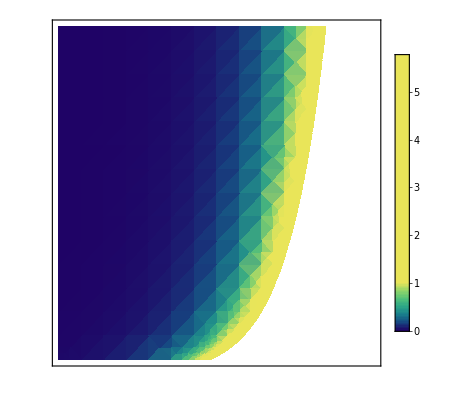

```mathematica
testEvUV0U={eC->10^-6,eD->10^-2,dMref->2 10^-4,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU00->10^5,EvU0->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testEvUV0U;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testEvUV0U;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testEvUV0U;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1EvV0U=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND2EvV0U=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND3EvV0U=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND4EvV0U=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
M3ecoEvV0U=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,20,25}]-NIntegrate[ΔSCecodM,{x,20,25}]]/Abs[NIntegrate[ΔSCecodM,{x,20,25}]],
{EvU,30,50},{VmU0,10^5,2 10^6},
RegionFunction->Function[{EvU,VmU0,z},Evaluate[Im[M3ecoEvV0U]==0&&M3ecoEvV0U>0&&COND1EvV0U>0&&COND2EvV0U>0&&COND3EvV0U>0&&COND4EvV0U>0]],
PlotRange->Full,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],ColorFunctionScaling->False,FrameTicks->None,PlotLegends->Automatic]
```

### Figure 2c

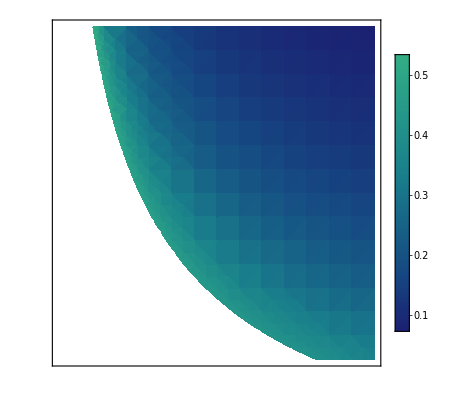

```mathematica
testT0c0={eC->10^-6,eD->10^-2,dMref->1.1 10^-3,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.09,γZ->0.4,c0->1.1131,x00->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testT0c0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testT0c0;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testT0c0;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1T0c0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND2T0c0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND3T0c0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND4T0c0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
M3ecoT0c0=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
RegionFunction->Function[{c,x0,z},Evaluate[Im[M3ecoT0c0]==0&&M3ecoT0c0>0&&COND1T0c0>0&&COND2T0c0>0&&COND3T0c0>0&&COND4T0c0>0]],
PlotRange->Full,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],ColorFunctionScaling->False,FrameTicks->None,PlotLegends->Automatic]
```

### Figure 2d

```mathematica
testT0c0={eC->10^-6,eD->10^-2,dMref->2 10^-4,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c0->1.1131,x00->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testT0c0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testT0c0;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testT0c0;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1T0c0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND2T0c0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND3T0c0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND4T0c0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
M3ecoT0c0=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
RegionFunction->Function[{c,x0,z},Evaluate[Im[M3ecoT0c0]==0&&M3ecoT0c0>0&&COND1T0c0>0&&COND2T0c0>0&&COND3T0c0>0&&COND4T0c0>0]],
PlotRange->Full,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],ColorFunctionScaling->False,FrameTicks->None,PlotLegends->Automatic]
```

-Graphics-

## Figure 3 (a-d)

### Figure 3a : EdM:0 (baseline scenario)

116.68

40.3494

22.4482

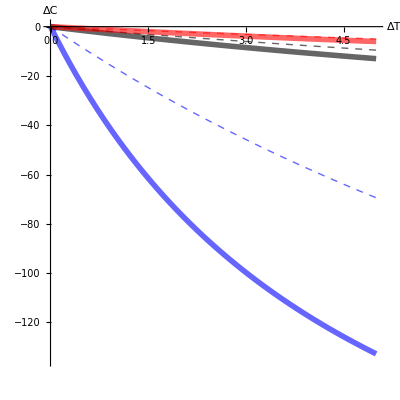

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-135,0}},
PlotStyle->{{Blue,Opacity[0.6],Dashed,Thick},{Blue,Opacity[0.6],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Black,Opacity[0.6],Dashed,Thick},{Black,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Red,Dashed,Opacity[0.6],Thick},{Red,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

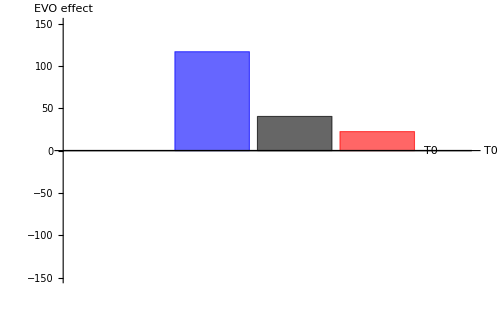

```mathematica
BarChart[{{116.7,40.3,22.4}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{Opacity[0.6],{Blue,Black,Red}},
ImageSize->500,AxesLabel->{"T0","EVO effect"} ]
```

### Figure 3b : EdM=25 (low mortality T-dependence)

21.4137

15.5178

12.6649

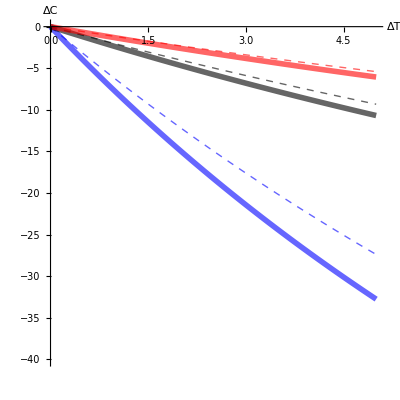

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-40,0}},PlotStyle->{{Blue,Opacity[0.6],Dashed,Thick},{Blue,Opacity[0.6],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Black,Opacity[0.6],Dashed,Thick},{Black,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Red,Opacity[0.6],Dashed,Thick},{Red,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

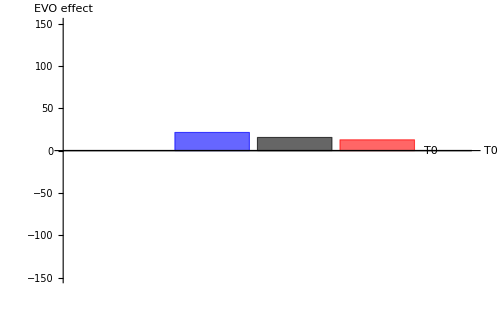

```mathematica
BarChart[{{21.4,15.5,12.7}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{Opacity[0.6],{Blue,Black,Red}},
ImageSize->500,AxesLabel->{"T0","EVO effect"} ]
```

### Figure 3b : EdM=55 (high mortality T-dependence)

13.6124

23.7831

34.8103

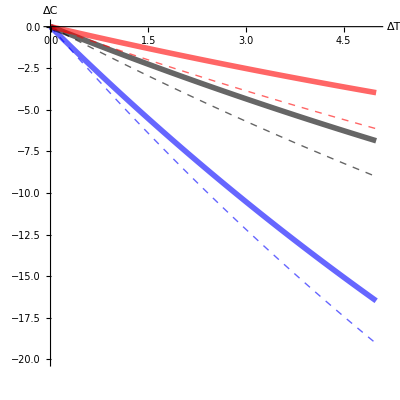

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-20,0}},PlotStyle->{{Blue,Opacity[0.6],Dashed,Thick},{Blue,Opacity[0.6],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Black,Opacity[0.6],Dashed,Thick},{Black,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Red,Opacity[0.6],Dashed,Thick},{Red,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

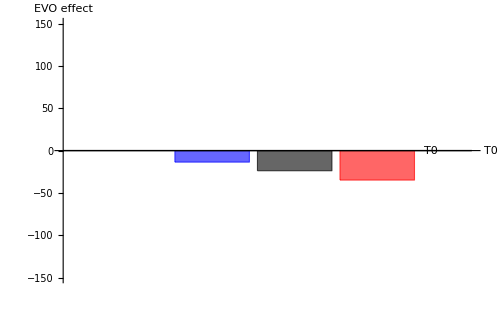

```mathematica
BarChart[{{-13.6,-23.8,-34.8}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{Opacity[0.6],{Blue,Black,Red}},
ImageSize->500,AxesLabel->{"T0","EVO effect"}]
```

### Figure 3d : m= - 0.014 (MGE T-dependence)

83.0005

6.73921

140.856

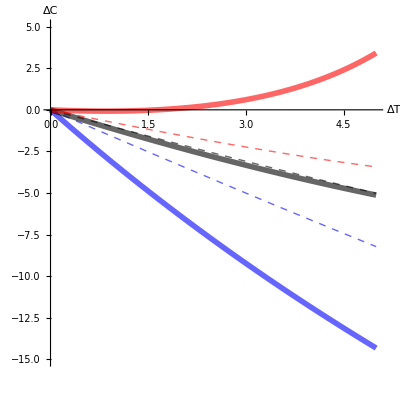

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-15,5}},PlotStyle->{{Blue,Opacity[0.6],Dashed,Thick},{Blue,Opacity[0.6],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},PlotStyle->{{Black,Opacity[0.6],Dashed,Thick},{Black,Opacity[0.6],Thickness[0.01]}},ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},PlotStyle->{{Red,Opacity[0.6],Dashed,Thick},{Red,Opacity[0.6],Thickness[0.01]}},ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

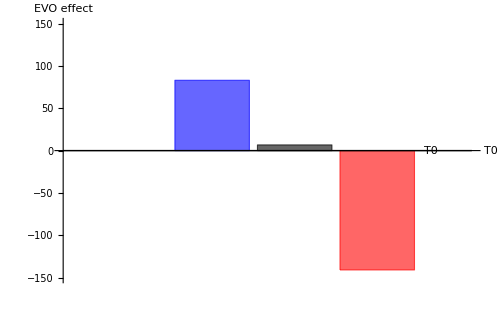

```mathematica
BarChart[{{83,6.7,-140.9}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{Opacity[0.6],{Blue,Black,Red}},
ImageSize->500,AxesLabel->{"T0","EVO effect"}]
```

## Figure 4 (a-d) (ECO)

### Figure 4a - Baseline scenario

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-170.872

-9.8851

-50.726

-31.7999

-36.0681

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-9.75727

-3.21334

-15.0353

-13.4817

-17.0721

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-5.59079

-2.14822

-9.8245

-9.44123

-12.2572

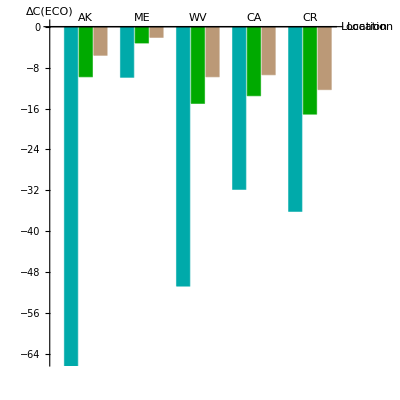

```mathematica
BarChart[{{-170.9,-9.8,-5.6},{-9.9,-3.2,-2.1},{-50.7,-15,-9.8},{-31.8,-13.5,-9.4},{-36.1,-17.1,-12.3}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{20,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECO)"}]
```

### Figure 4b - Low mortality T-dependence (EdM = 25)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-15.2163

-5.44244

-32.4465

-29.2713

-38.3475

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-5.49483

-2.44518

-12.3667

-12.7386

-17.4934

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-3.69634

-1.73152

-8.4134

-8.94598

-12.4342

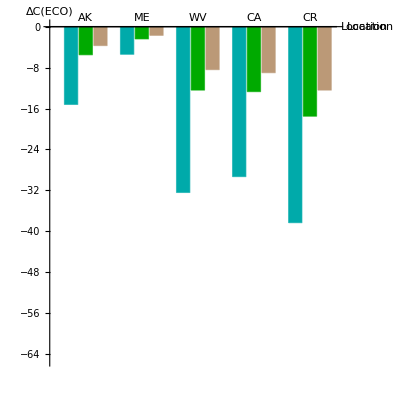

```mathematica
BarChart[{{-15.2,-5.5,-3.7},{-5.4,-2.4,-1.7},{-32.4,-12.4,-8.4},{-29.3,-12.7,-9},{-38.3,-17.5,-12.4}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{20,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECO)"}]
```

### Figure 4c - High mortality T-dependence (EdM = 55)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-9.63332

-4.1612

-25.0055

-26.8456

-42.073

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-4.42801

-2.11158

-10.8518

-11.9809

-17.9883

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-3.13527

-1.53933

-7.57721

-8.43361

-12.5596

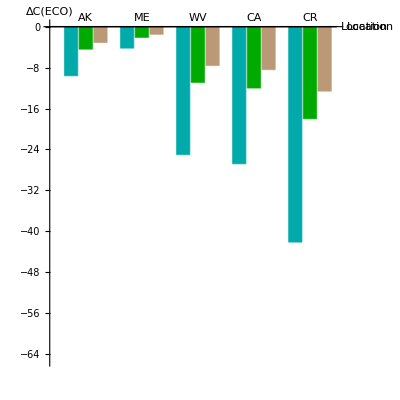

```mathematica
BarChart[{{-9.6,-4.4,-3.1},{-4.2,-2.1,-1.5},{-25,-10.9,-7.6},{-26.8,-12,-8.4},{-42.1,-18,-12.6}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{20,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECO)"}]
```

### Figure 4d - MGE T-dependence

```mathematica
γMx=γMref+m(x-xref);
φγMx=φx/.γM->γMx;
φγMT0=φγMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014/.x->x0;
SC3ecoγMx=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014;
SC3ecoevoγMx=SC3ecox/.φ->φx/.γM->γMx/.m->-0.014;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-0.729677

-1.67335

-11.6027

-14.0385

-33.1057

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-0.652151

-0.928154

-5.2073

-6.76087

-14.7635

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-0.711518

-0.754988

-3.9722

-5.10773

-10.5303

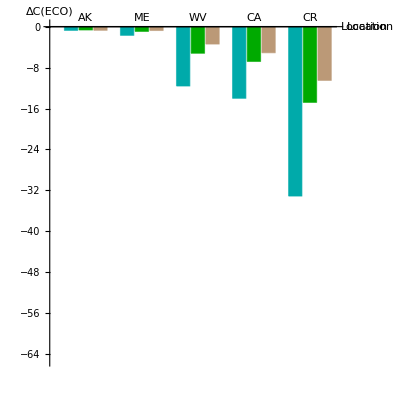

```mathematica
BarChart[{{-0.73,-0.65,-0.71},{-1.7,-0.93,-0.75},{-11.6,-5.2,-3.4},{-14,-6.8,-5.1},{-33.1,-14.8,-10.5}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{20,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECO)"} ]
```

## Figure 4 (e-h) (ECOEVO)

### Figure 4e - Baseline scenario

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-556.028

-24.072

-92.7902

-47.3891

-41.996

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-21.7836

-5.07653

-21.3065

-16.8857

-18.5883

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-10.3186

-3.01212

-12.8012

-11.1972

-13.0723

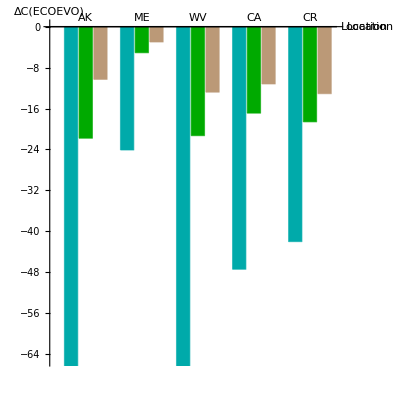

```mathematica
BarChart[{{-556,-21.8,-10.3},{-24.1,-5.1,-3},{-92.8,-21.3,-12.8},{-47.4,-16.9,-11.2},{-42,-18.6,-13.1}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{30,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECOEVO)"}]
```

### Figure 4f - Low mortality T-dependence (EdM = 25)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-20.7003

-6.6998

-38.6089

-34.1117

-41.3944

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-6.50917

-2.71754

-13.5996

-13.8228

-18.219

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-4.1998

-1.87175

-9.03621

-9.50865

-12.8166

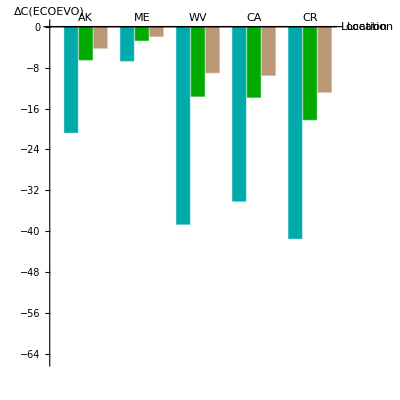

```mathematica
BarChart[{{-20.7,-6.5,-4.2},{-6.7,-2.7,-1.9},{-38.6,-13.6,-9},{-34.1,-13.8,-9.5},{-41.4,-18.2,-12.8}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{30,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECOEVO)"}]
```

### Figure 4g - High mortality T-dependence (EdM = 55)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-7.99328

-3.5669

-21.1507

-21.1325

-34.9554

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-4.00157

-1.95213

-9.93497

-10.6708

-16.5079

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-2.90481

-1.45244

-7.09366

-7.74966

-11.8061

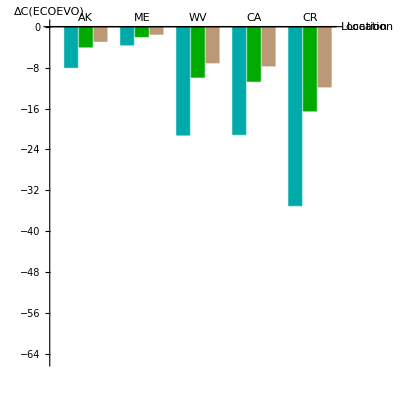

```mathematica
BarChart[{{-8,-4,-2.9},{-3.6,-2,-1.5},{-21.2,-9.9,-7.1},{-21.1,-10.7,-7.7},{-35,-16.5,-11.8}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{30,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECOEVO)"} ]
```

### Figure 4h - MGE T-dependence

```mathematica
γMx=γMref+m(x-xref);
φγMx=φx/.γM->γMx;
φγMT0=φγMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014/.x->x0;
SC3ecoγMx=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014;
SC3ecoevoγMx=SC3ecox/.φ->φx/.γM->γMx/.m->-0.014;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-7.95763

-3.17771

-17.8918

-16.9246

-27.587

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-1.94902

-1.25094

-6.50224

-7.40929

-13.5531

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-1.35045

-0.920725

-4.63062

-5.44451

-9.90564

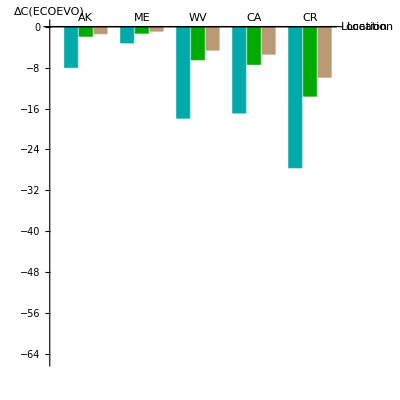

```mathematica
BarChart[{{-8,-1.9,-1.4},{-3.2,-1.3,-0.9},{-17.9,-6.5,-4.6},{-16.9,-7.4,-5.4},{-27.6,-13.6,-9.9}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{30,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECOEVO)"} ]
```

## Figure 4 (i-l) (ECOEVO) Note: we calculate the norm of the EVO effect (sign comes from comparing ECO and ECOEVO)

### Figure 4i - Baseline scenario

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.17};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

225.406

143.518

82.9245

49.0225

16.4354

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.34};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

123.255

57.9828

41.7093

25.2491

8.88161

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.5};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

84.565

40.2143

30.2986

18.5993

6.64983

```mathematica
dataEVO1={{0.1,225.4},{5,143.5},{9,82.9},{17,49},{26,16.4}};
dataEVO2={{0.1,123.3},{5,58},{9,41.7},{17,25.2},{26,8.9}};
dataEVO3={{0.1,84.6},{5,40.2},{9,30.3},{17,18.6},{26,6.6}};
```

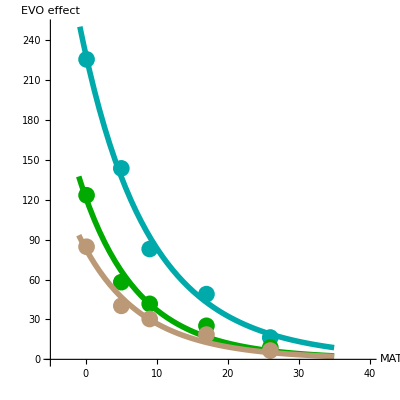

```mathematica
Off[NonlinearModelFit::cvmit]
dataEVO={{0.1,225.4},{5,143.5},{9,82.9},{17,49},{26,16.4}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot1=Show[Plot[nlmEVO[x],{x,-1,35},PlotRange->{{-5,40},{0,250}},AxesOrigin->{-5,0},PlotStyle->{Darker[Cyan],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Cyan],PointSize[0.03]}],AspectRatio->1,AxesLabel->{"MAT","EVO effect"}];
dataEVO={{0.1,123.3},{5,58},{9,41.7},{17,25.2},{26,8.9}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot2=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Darker[Green],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Green],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
dataEVO={{0.1,84.6},{5,40.2},{9,30.3},{17,18.6},{26,6.6}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot3=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Lighter[Brown],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Lighter[Brown],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
Show[Plot1,Plot2,Plot3]
```

### Figure 4j - Low mortality T-dependence (EdM = 25)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.17};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

36.0401

23.1028

18.9924

16.5361

7.94549

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.34};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

18.4599

11.1387

9.96915

8.51048

4.14794

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.5};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

13.6204

8.09905

7.40261

6.28965

3.07578

```mathematica
dataEVO4={{0.1,36},{5,23.1},{9,19},{17,16.5},{26,7.9}};
dataEVO5={{0.1,18.5},{5,11.1},{9,10},{17,8.5},{26,4.1}};
dataEVO6={{0.1,13.6},{5,8.1},{9,7.4},{17,6.3},{26,3.1}};
```

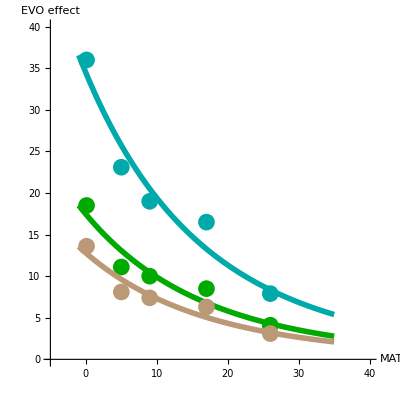

```mathematica
Off[NonlinearModelFit::cvmit]
dataEVO={{0.1,36},{5,23.1},{9,19},{17,16.5},{26,7.9}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot1=Show[Plot[nlmEVO[x],{x,-1,35},PlotRange->{{-5,40},{0,40}},AxesOrigin->{-5,0},PlotStyle->{Darker[Cyan],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Cyan],PointSize[0.03]}],AspectRatio->1,AxesLabel->{"MAT","EVO effect"}];
dataEVO={{0.1,18.5},{5,11.1},{9,10},{17,8.5},{26,4.1}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot2=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Darker[Green],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Green],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
dataEVO={{0.1,13.6},{5,8.1},{9,7.4},{17,6.3},{26,3.1}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot3=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Lighter[Brown],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Lighter[Brown],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
Show[Plot1,Plot2,Plot3]
```

### Figure 4k - High mortality T-dependence (EdM = 55)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.17};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

17.0247

14.2821

15.4156

21.2815

16.9172

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.34};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

9.63055

7.55109

8.44883

10.9349

8.22986

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.5};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

7.35043

5.6451

6.38159

8.1098

5.99928

```mathematica
dataEVO7={{0.1,-17},{5,-14.3},{9,-15.4},{17,-21.3},{26,-16.9}};
dataEVO8={{0.1,-9.6},{5,-7.6},{9,-8.4},{17,-10.9},{26,-8.2}};
dataEVO9={{0.1,-7.4},{5,-5.6},{9,-6.4},{17,-8.1},{26,-6}};
```

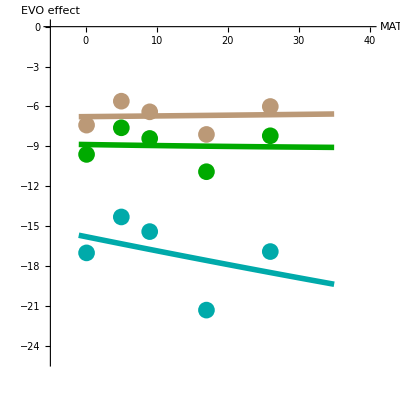

```mathematica
Off[NonlinearModelFit::cvmit]
dataEVO={{0.1,-17},{5,-14.3},{9,-15.4},{17,-21.3},{26,-16.9}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot1=Show[Plot[nlmEVO[x],{x,-1,35},PlotRange->{{-5,40},{-25,0}},AxesOrigin->{-5,0},PlotStyle->{Darker[Cyan],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Cyan],PointSize[0.03]}],AspectRatio->1,AxesLabel->{"MAT","EVO effect"}];
dataEVO={{0.1,-9.6},{5,-7.6},{9,-8.4},{17,-10.9},{26,-8.2}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot2=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Darker[Green],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Green],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
dataEVO={{0.1,-7.4},{5,-5.6},{9,-6.4},{17,-8.1},{26,-6}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot3=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Lighter[Brown],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Lighter[Brown],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
Show[Plot1,Plot2,Plot3]
```

### Figure 4l - MGE T-dependence

```mathematica
γMx=γMref+m(x-xref);
φγMx=φx/.γM->γMx;
φγMT0=φγMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014/.x->x0;
SC3ecoγMx=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014;
SC3ecoevoγMx=SC3ecox/.φ->φx/.γM->γMx/.m->-0.014;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
dataEVO7={{0.1,990.6},{5,89.9},{9,54.2},{17,20.6},{26,-16.7}};
dataEVO8={{0.1,198.9},{5,34.8},{9,24.9},{17,9.6},{26,-8.2}};
dataEVO9={{0.1,89.8},{5,22},{9,16.6},{17,6.6},{26,-5.9}};
```

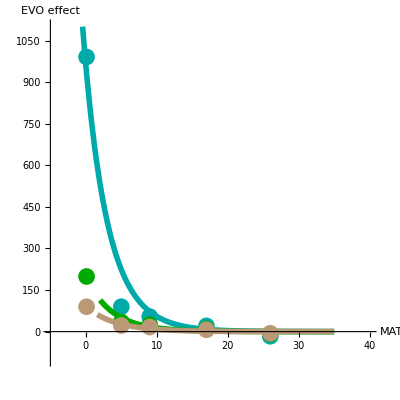

```mathematica
Off[NonlinearModelFit::cvmit]
dataEVO={{0.1,990.6},{5,89.9},{9,54.2},{17,20.6},{26,-16.7}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot1=Show[Plot[nlmEVO[x],{x,-1,35},PlotRange->{{-5,40},{-100,1100}},AxesOrigin->{-5,0},PlotStyle->{Darker[Cyan],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Cyan],PointSize[0.03]}],AspectRatio->1,AxesLabel->{"MAT","EVO effect"}];
dataEVO={{0.1,198.9},{5,34.8},{9,24.9},{17,9.6},{26,-8.2}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot2=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Darker[Green],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Green],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
dataEVO={{0.1,89.8},{5,22},{9,16.6},{17,6.6},{26,-5.9}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot3=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Lighter[Brown],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Lighter[Brown],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
Show[Plot1,Plot2,Plot3]
```

## Supplementary Figure 2

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-4,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->7.3 10^5,EvU->35,x->20};
COND1φ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2φ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3φ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4φ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoφ=M3ecox/.testparam;
```

### Supplementary Figure 2a (M)

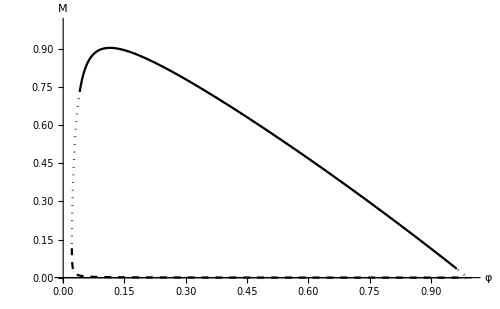

```mathematica
Plot1=Plot[{Meq1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,1}},
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","M"}];
Plot2=Plot[{Meq2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam,M3ecox/.testparam},
{φ,0.02,0.99},PlotRange->{{0,1},{0,1}},
PlotStyle->{{Black,Dashed},{Black,Dotted}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Plot3=Plot[{M3ecox/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,1}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoφ]==0&&M3ecoφ>0&&COND1φ>0&&COND2φ>0&&COND3φ>0&&COND4φ>0]],
PlotStyle->{{Black}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot1,Plot3,Plot2]
```

### Supplementary Figure 2b (Z)

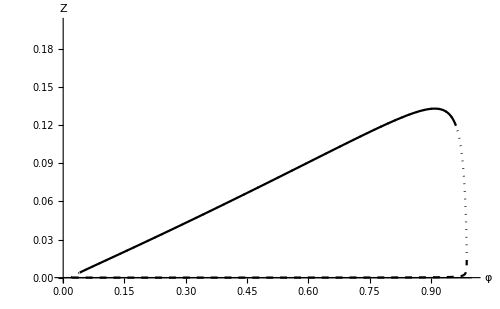

```mathematica
Plot1=Plot[{Zeq1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,0.2}},
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","Z"}];
Plot2=Plot[{Zeq2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam,Z3ecox/.testparam},
{φ,0.02,0.99},PlotRange->{{0,1},{0,0.2}},
PlotStyle->{{Black,Dashed},{Black,Dotted}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Plot3=Plot[{Z3ecox/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,0.2}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoφ]==0&&M3ecoφ>0&&COND1φ>0&&COND2φ>0&&COND3φ>0&&COND4φ>0]],
PlotStyle->{{Black}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot1,Plot3,Plot2]
```

### Supplementary Figure 2c

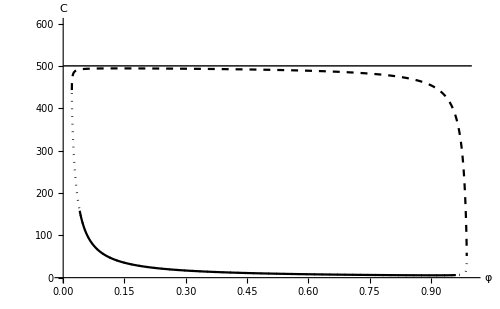

```mathematica
Plot1=Plot[{SCeq1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,600}},
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","C"}];
Plot2=Plot[{SCeq2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam,SC3ecox/.testparam},
{φ,0.02,0.99},PlotRange->{{0,1},{0,600}},
PlotStyle->{{Black,Dashed},{Black,Dotted}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Plot3=Plot[{SC3ecox/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,600}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoφ]==0&&M3ecoφ>0&&COND1φ>0&&COND2φ>0&&COND3φ>0&&COND4φ>0]],
PlotStyle->{{Black}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot1,Plot3,Plot2]
```

### Supplementary Figure 2d (D)

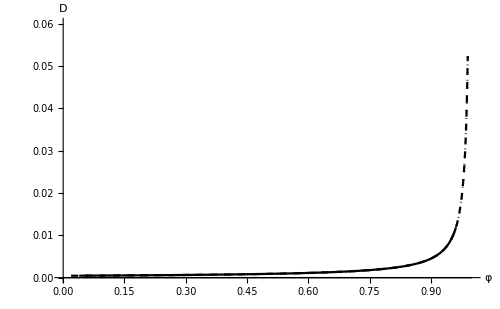

```mathematica
Plot1=Plot[{DCeq1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,0.06}},
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","D"}];
Plot2=Plot[{DCeq2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam,DC3ecox/.testparam},
{φ,0.02,0.99},PlotRange->{{0,1},{0,0.06}},
PlotStyle->{{Black,Dashed},{Black,Dotted}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Plot3=Plot[{DC3ecox/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,0.06}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoφ]==0&&M3ecoφ>0&&COND1φ>0&&COND2φ>0&&COND3φ>0&&COND4φ>0]],
PlotStyle->{{Black}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot1,Plot3,Plot2]
```

## Supplementary Figure 3

### Supplementary Figure 3a (γM)

### default

```mathematica
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,x->20};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
Plot0=Plot[SC3ecox/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,200}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black}}];
```

### min/max

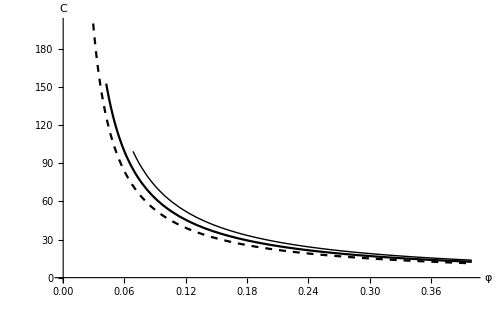

```mathematica
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.2,γZ->0.4,x->20};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
PlotA=Plot[SC3ecox/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,200}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","C"}];
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.4,γZ->0.4,x->20};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
PlotB=Plot[SC3ecox/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,200}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black,Dashed}}];
Show[PlotA,Plot0,PlotB]
```

## Supplementary Figure 4

### Supplementary Figure 4a (γM)

### default

```mathematica
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,φ->0.1};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
Plot0=Plot[SC3ecox/.testparam,{x,0,40},PlotRange->{{0,40},{0,200}},
RegionFunction->Function[{x,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black}}];
```

### min/max

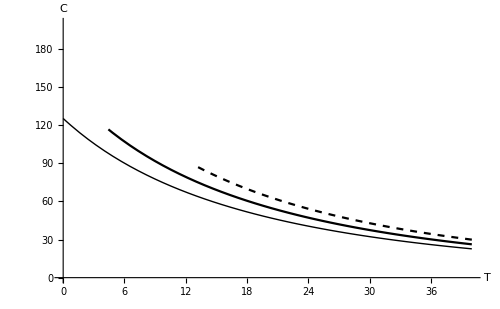

```mathematica
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.2,γZ->0.4,φ->0.1};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
PlotA=Plot[SC3ecox/.testparam,{x,0,40},PlotRange->{{0,40},{0,200}},
RegionFunction->Function[{x,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black,Dashed}},ImageSize->500,AxesLabel->{"T","C"}];
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.4,γZ->0.4,φ->0.1};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
PlotB=Plot[SC3ecox/.testparam,{x,0,40},PlotRange->{{0,40},{0,200}},
RegionFunction->Function[{x,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black,Thick}}];
Show[PlotA,Plot0,PlotB]
```

## Supplementary Figure 5

### Supplementary Figure 5a and Supplementary Figure 5e

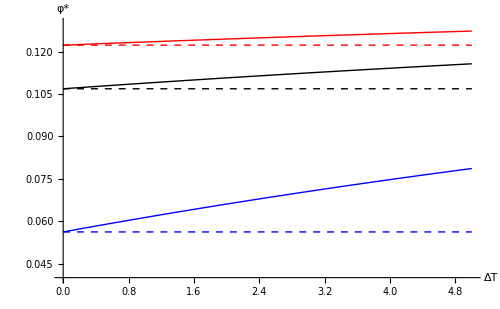

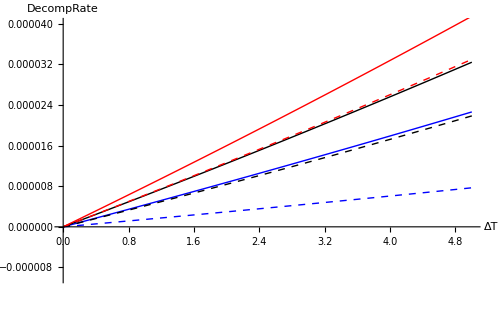

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
txdecompx=VmD Z/(KmD+SC)/.Z->Zeq3/.SC->SCeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+dx;
txdecompadaptT0=txdecompx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
txdecompecodMx=txdecompx/.φ->φdMT0/.dM->dMx/.testparam;
txdecompecoevodMx=txdecompx/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔecotxdecompdM=txdecompecodMx-txdecompadaptT0;
ΔecoevotxdecompdM=txdecompecoevodMx-txdecompadaptT0;
Plot1=Plot[{φdMT0/.testparam,φdMx/.testparam},{dx,0,5},AxesOrigin->{0,0.04},PlotRange->{{0,5},{0.04,0.13}},PlotStyle->{{Blue,Dashed,Thick},{Blue,Thick}},ImageSize->500,AxesLabel->{"ΔT","φ*"}];
Plot2=Plot[{ΔecotxdecompdM,ΔecoevotxdecompdM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-10^-5,4 10^-5}},PlotStyle->{{Blue,Dashed,Thick},{Blue,Thick}},ImageSize->500,AxesLabel->{"ΔT","DecompRate"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
txdecompx=VmD Z/(KmD+SC)/.Z->Zeq3/.SC->SCeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+dx;
txdecompadaptT0=txdecompx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
txdecompecodMx=txdecompx/.φ->φdMT0/.dM->dMx/.testparam;
txdecompecoevodMx=txdecompx/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔecotxdecompdM=txdecompecodMx-txdecompadaptT0;
ΔecoevotxdecompdM=txdecompecoevodMx-txdecompadaptT0;
Plot3=Plot[{φdMT0/.testparam,φdMx/.testparam},{dx,0,5},PlotStyle->{{Black,Dashed,Thick},{Black,Thick}},ImageSize->500];
Plot4=Plot[{ΔecotxdecompdM,ΔecoevotxdecompdM},{dx,0,5},PlotStyle->{{Black,Dashed,Thick},{Black,Thick}},ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
txdecompx=VmD Z/(KmD+SC)/.Z->Zeq3/.SC->SCeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+dx;
txdecompadaptT0=txdecompx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
txdecompecodMx=txdecompx/.φ->φdMT0/.dM->dMx/.testparam;
txdecompecoevodMx=txdecompx/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔecotxdecompdM=txdecompecodMx-txdecompadaptT0;
ΔecoevotxdecompdM=txdecompecoevodMx-txdecompadaptT0;
Plot5=Plot[{φdMT0/.testparam,φdMx/.testparam},{dx,0,5},PlotStyle->{{Red,Dashed,Thick},{Red,Thick}},ImageSize->500];
Plot6=Plot[{ΔecotxdecompdM,ΔecoevotxdecompdM},{dx,0,5},PlotStyle->{{Red,Dashed,Thick},{Red,Thick}},ImageSize->500];
Show[Plot1,Plot3,Plot5]
Show[Plot2,Plot4,Plot6]
```

## Supplementary Figure 6

### Supplementary Figure 6a1

53.2635

22.2288

12.4011

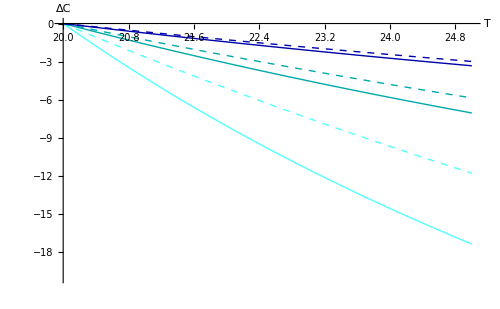

```mathematica
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.25,γZ->0.4,c->1.17,x0->20};
Abs[NIntegrate[ΔSCecoevo/.x->x0+dx/.testparam,{dx,0,5}]-NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]/Abs[NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]*100
Plot1=Plot[{ΔSCeco/.testparam/.x0->20,ΔSCecoevo/.testparam/.x0->20},{x,20,25},AxesOrigin->{20,0},PlotRange->{{20,25},{-20,0}},PlotStyle->{{Lighter[Cyan],Dashed,Thick},{Lighter[Cyan],Thick}},ImageSize->500,AxesLabel->{"T","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.5,γZ->0.4,c->1.17,x0->20};
Abs[NIntegrate[ΔSCecoevo/.x->x0+dx/.testparam,{dx,0,5}]-NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]/Abs[NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]*100
Plot2=Plot[{ΔSCeco/.testparam/.x0->20,ΔSCecoevo/.testparam/.x0->20},{x,20,25},PlotStyle->{{Darker[Cyan],Dashed,Thick},{Darker[Cyan],Thick}}];
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.75,γZ->0.4,c->1.17,x0->20};
Abs[NIntegrate[ΔSCecoevo/.x->x0+dx/.testparam,{dx,0,5}]-NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]/Abs[NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]*100
Plot3=Plot[{ΔSCeco/.testparam/.x0->20,ΔSCecoevo/.testparam/.x0->20},{x,20,25},PlotStyle->{{Darker[Blue],Dashed,Thick},{Darker[Blue],Thick}}];
Show[Plot1,Plot2,Plot3]
```

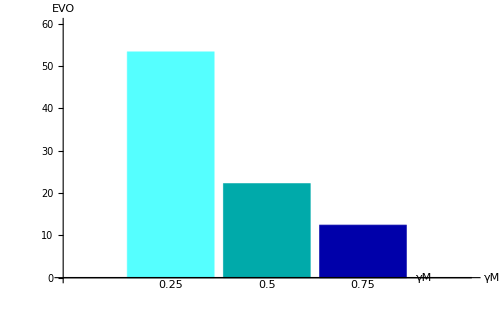

```mathematica
BarChart[{{53.3,22.2,12.4}},
ChartLabels->{"0.25","0.5","0.75"},
AxesLabel->{"γM","EVO"},
PlotRange->{Automatic,{0,60}},
ChartStyle->{Lighter[Cyan],Darker[Cyan],Darker[Blue]},
ImagePadding->{{20,40},{15,20}},ImageSize->500 ]
```

### Supplementary Figure 6a2

```mathematica
testxone={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM0->0.3,γZ->0.4,c->1.17,x0->20};
LPx=0.25;
HPx=0.75;
LOx=ΔSCeco/.x->x0+dx/.dx->5/.testxone/.γM->LPx;
HOx=ΔSCeco/.x->x0+dx/.dx->5/.testxone/.γM->HPx;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

1.24923

```mathematica
LOx=ΔSCecoevo/.x->x0+dx/.dx->5/.testxone/.γM->LPx;
HOx=ΔSCecoevo/.x->x0+dx/.dx->5/.testxone/.γM->HPx;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

1.50386

```mathematica
LOx=Abs[NIntegrate[ΔSCecoevo/.x->x0+dx/.γM->LPx/.testxone,{dx,0,5}]-NIntegrate[ΔSCeco/.x->x0+dx/.γM->LPx/.testxone,{dx,0,5}]]/Abs[NIntegrate[ΔSCeco/.x->x0+dx/.γM->LPx/.testxone,{dx,0,5}]]*100;
HOx=Abs[NIntegrate[ΔSCecoevo/.x->x0+dx/.γM->HPx/.testxone,{dx,0,5}]-NIntegrate[ΔSCeco/.x->x0+dx/.γM->HPx/.testxone,{dx,0,5}]]/Abs[NIntegrate[ΔSCeco/.x->x0+dx/.γM->HPx/.testxone,{dx,0,5}]]*100;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

1.32664

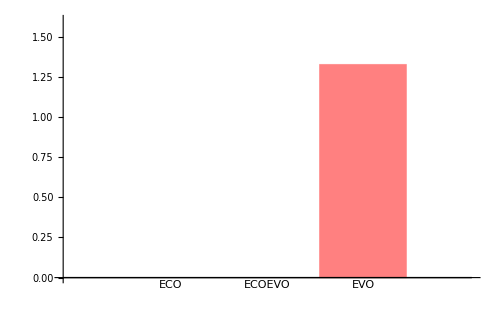

```mathematica
BarChart[{{1.249232907351444,1.5038615204491705,1.3266426887693321}},
ChartLabels->{"ECO","ECOEVO","EVO"},
PlotRange->{Automatic,{0,1.6}},
ChartStyle->{Directive[EdgeForm[{Thickness[0.005],AbsoluteDashing[{5,15-5}]}],White],Directive[EdgeForm[Thickness[0.005]],White],Pink},
ImagePadding->{{20,40},{15,20}},ImageSize->500 ]
```

## Supplementary Figure 7

### Supplementary Figure 7a

```mathematica
testv0DEvD={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD00->1.15 10^6,EvD0->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20};
COND1γZdZ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testv0DEvD;
COND2γZdZ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testv0DEvD;
COND3γZdZ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testv0DEvD;
COND4γZdZ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testv0DEvD;
M3ecoγZdZ=M3ecox/.φ->φx/.x->x0/.testv0DEvD;
```

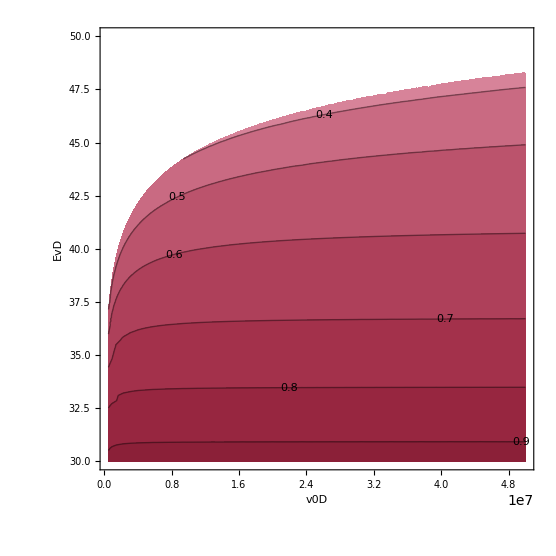

```mathematica
ContourPlot[Abs[NIntegrate[ΔSCecoevo/.testv0DEvD,{x,20,25}]-NIntegrate[ΔSCeco/.testv0DEvD,{x,20,25}]]/Abs[NIntegrate[ΔSCeco/.testv0DEvD,{x,20,25}]],
{VmD0,5 10^5,5 10^7},{EvD,30,50},
RegionFunction->Function[{VmD0,EvD,z},Evaluate[Im[M3ecoγZdZ]==0&&M3ecoγZdZ>0&&COND1γZdZ>0&&COND2γZdZ>0&&COND3γZdZ>0&&COND4γZdZ>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"EvD",},{"v0D",}},LabelStyle->Directive[FontSize->20]]
```

### Supplementary Figure 7b

```mathematica
testK0DEKD={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD00->3.3 10^4,EkD0->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20};
COND1γZdZ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testK0DEKD;
COND2γZdZ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testK0DEKD;
COND3γZdZ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testK0DEKD;
COND4γZdZ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testK0DEKD;
M3ecoγZdZ=M3ecox/.φ->φx/.x->x0/.testK0DEKD;
```

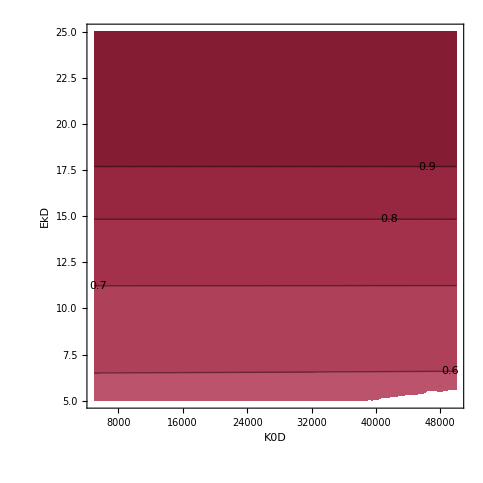

```mathematica
ContourPlot[Abs[NIntegrate[ΔSCecoevo/.testK0DEKD,{x,20,25}]-NIntegrate[ΔSCeco/.testK0DEKD,{x,20,25}]]/Abs[NIntegrate[ΔSCeco/.testK0DEKD,{x,20,25}]],
{KmD0,5 10^3,5 10^4},{EkD,5,25},
RegionFunction->Function[{KmD0,EkD,z},Evaluate[Im[M3ecoγZdZ]==0&&M3ecoγZdZ>0&&COND1γZdZ>0&&COND2γZdZ>0&&COND3γZdZ>0&&COND4γZdZ>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"EkD",},{"K0D",}},LabelStyle->Directive[FontSize->20]]
```

### Supplementary Figure 7c

```mathematica
testγZdZ={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ0->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ0->0.4,c->1.1131,x0->20};
COND1γZdZ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testγZdZ;
COND2γZdZ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testγZdZ;
COND3γZdZ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testγZdZ;
COND4γZdZ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testγZdZ;
M3ecoγZdZ=M3ecox/.φ->φx/.x->x0/.testγZdZ;
```

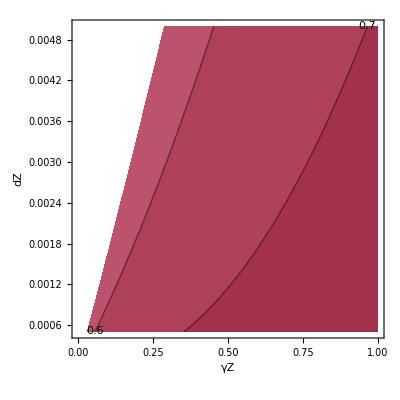

```mathematica
ContourPlot[Abs[NIntegrate[ΔSCecoevo/.testγZdZ,{x,20,25}]-NIntegrate[ΔSCeco/.testγZdZ,{x,20,25}]]/Abs[NIntegrate[ΔSCeco/.testγZdZ,{x,20,25}]],
{γZ,0,1},{dZ,5 10^-4,5 10^-3},
RegionFunction->Function[{γZ,dZ,z},Evaluate[Im[M3ecoγZdZ]==0&&M3ecoγZdZ>0&&COND1γZdZ>0&&COND2γZdZ>0&&COND3γZdZ>0&&COND4γZdZ>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"dZ",},{"γZ",}},LabelStyle->Directive[FontSize->20]]
```

### Supplementary Figure 7d

```mathematica
testISeD={eC->10^-6,eD0->10^-2,dM->2 10^-4,dZ->2 10^-3,IS0->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20};
COND1ISeD=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testISeD;
COND2ISeD=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testISeD;
COND3ISeD=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testISeD;
COND4ISeD=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testISeD;
M3ecoISeD=M3ecox/.φ->φx/.x->x0/.testISeD;
```

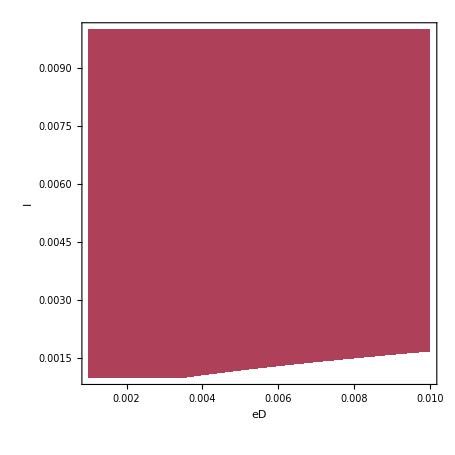

```mathematica
ContourPlot[Abs[NIntegrate[ΔSCecoevo/.testISeD,{x,20,25}]-NIntegrate[ΔSCeco/.testISeD,{x,20,25}]]/Abs[NIntegrate[ΔSCeco/.testISeD,{x,20,25}]],
{eD,10^-3,10^-2},{IS,10^-3,10^-2},
RegionFunction->Function[{eD,IS,z},Evaluate[Im[M3ecoISeD]==0&&M3ecoISeD>0&&COND1ISeD>0&&COND2ISeD>0&&COND3ISeD>0&&COND4ISeD>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"I",},{"eD",}},LabelStyle->Directive[FontSize->20]]
```

## Supplementary Figure 8

### Supplementary Figure 8a

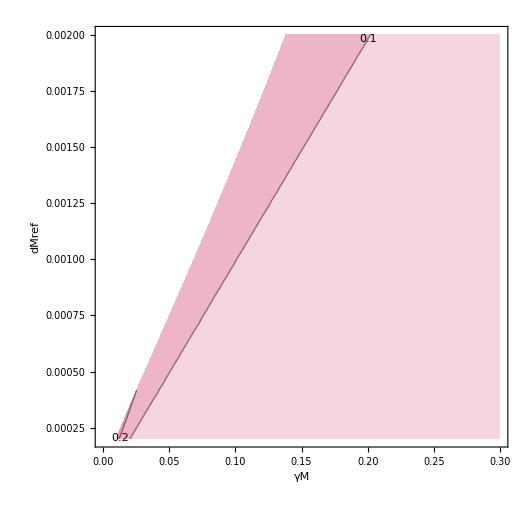

```mathematica
Off[Power::infy]
Off[Infinity::indet]
testgmdm={eC->10^-6,eD->10^-2,dM0->2 10^-4,EadM->25,dZ->2 10^-3,IS->5 10^-3,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM0->0.31,γZ->0.4,c->1.1131,x0->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testgmdm;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testgmdm;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testgmdm;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1gmdm=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND2gmdm=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND3gmdm=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND4gmdm=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
M3ecogmdm=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
Plot2=ContourPlot[Abs[NIntegrate[ΔSCecoevodM,{x,20,25}]-NIntegrate[ΔSCecodM,{x,20,25}]]/Abs[NIntegrate[ΔSCecodM,{x,20,25}]],
{γM,0,0.3},{dMref,2 10^-4,2 10^-3},
RegionFunction->Function[{γM,dMref,z},Evaluate[Im[M3ecogmdm]==0&&M3ecogmdm>0&&COND1gmdm>0&&COND2gmdm>0&&COND3gmdm>0&&COND4gmdm>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"dMref",},{"γM",}},LabelStyle->Directive[FontSize->20]]
```

### Supplementary Figure 8b

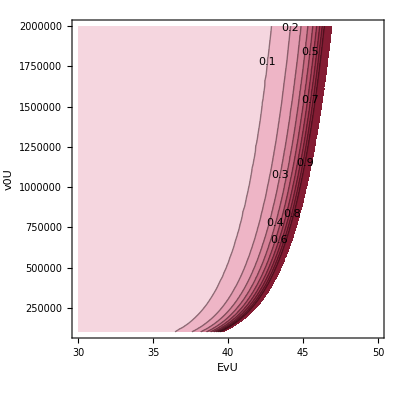

```mathematica
testEvUV0U={eC->10^-6,eD->10^-2,dMref->2 10^-4,EadM->25,dZ->2 10^-3,IS->5 10^-3,VmU00->10^5,EvU0->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testEvUV0U;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testEvUV0U;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testEvUV0U;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1EvV0U=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND2EvV0U=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND3EvV0U=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND4EvV0U=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
M3ecoEvV0U=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
ContourPlot[Abs[NIntegrate[ΔSCecoevodM,{x,20,25}]-NIntegrate[ΔSCecodM,{x,20,25}]]/Abs[NIntegrate[ΔSCecodM,{x,20,25}]],
{EvU,30,50},{VmU0,10^5,2 10^6},
RegionFunction->Function[{EvU,VmU0,z},Evaluate[Im[M3ecoEvV0U]==0&&M3ecoEvV0U>0&&COND1EvV0U>0&&COND2EvV0U>0&&COND3EvV0U>0&&COND4EvV0U>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"v0U",},{"EvU",}},LabelStyle->Directive[FontSize->20]]
```

## Supplementary Figure 9

### Supplementary Figure 9a

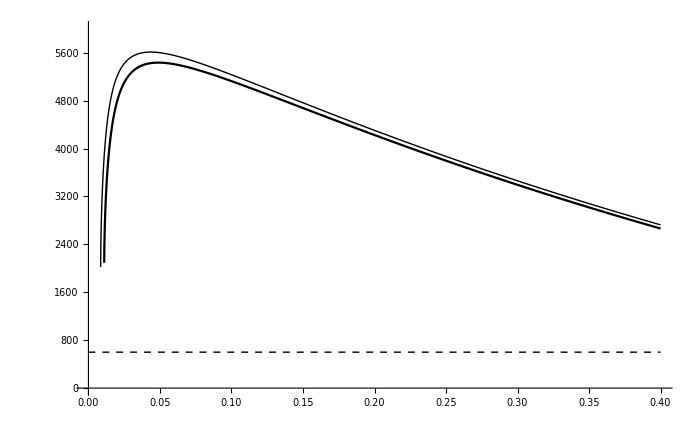

```mathematica
testparam={IS->3 10^-3,VmU0->4 10^3,EvU->46,dM->10^-6,eC->5 10^-6,γM->0.7,eD->10^-2,dZ->2 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,T0->20};
COND1paramT0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND2paramT0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND3paramT0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND4paramT0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
M3ecoparamT0=M3ecox/.x->T0/.testparam;
COND1paramT1=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+5/.testparam;
COND2paramT1=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+5/.testparam;
COND3paramT1=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+5/.testparam;
COND4paramT1=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+5/.testparam;
M3ecoparamT1=M3ecox/.x->T0+5/.testparam;
Plot2a=Plot[SC3ecox+M3ecox+Z3ecox+DC3ecox/.x->T0+5/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,6000}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamT1]==0&&M3ecoparamT1>0&&COND1paramT1>0&&COND2paramT1>0&&COND3paramT1>0&&COND4paramT1>0]],
PlotStyle->{Black,Thick},LabelStyle->Directive[FontSize->20],ImageSize->700];
Plot2b=Plot[SC3ecox+M3ecox+Z3ecox+DC3ecox/.x->T0/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,6000}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamT0]==0&&M3ecoparamT0>0&&COND1paramT0>0&&COND2paramT0>0&&COND3paramT0>0&&COND4paramT0>0]],
PlotStyle->{Black}];
Plot2c=Plot[SCeq1/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,6000}},PlotStyle->{Black,Dashed,Thick}];
Show[Plot2a,Plot2b,Plot2c]
```

### Supplementary Figure 9b

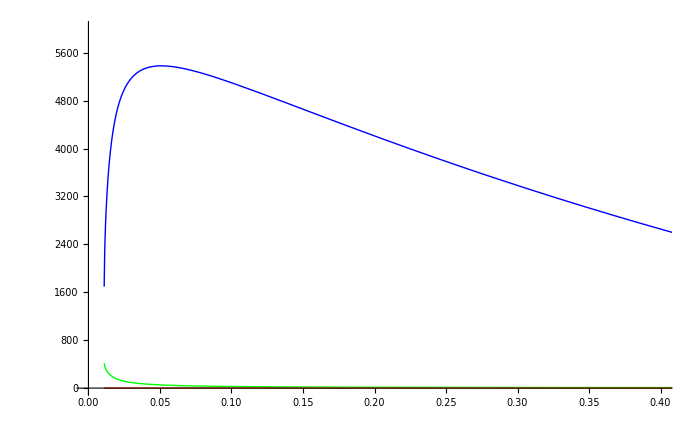

```mathematica
testparam={IS->3 10^-3,VmU0->4 10^3,EvU->46,dM->10^-6,eC->5 10^-6,γM->0.7,eD->10^-2,dZ->2 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,T0->20};
COND1paramT0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND2paramT0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND3paramT0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND4paramT0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
M3ecoparamT0=M3ecox/.x->T0/.testparam;
Plot1=Plot[{M3ecox/.x->T0/.testparam,Z3ecox/.x->T0/.testparam,SC3ecox/.x->T0/.testparam,DC3ecox/.x->T0/.testparam},{φ,0,1},PlotRange->{{0,0.4},{0,6000}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamT0]==0&&M3ecoparamT0>0&&COND1paramT0>0&&COND2paramT0>0&&COND3paramT0>0&&COND4paramT0>0]],
PlotStyle->{{Blue,Thick},{Magenta,Thick},{Green,Thick},{Orange,Thick}},LabelStyle->Directive[FontSize->20],ImageSize->700]
```

## Supplementary Figure 10

### Supplementary Figure 10a

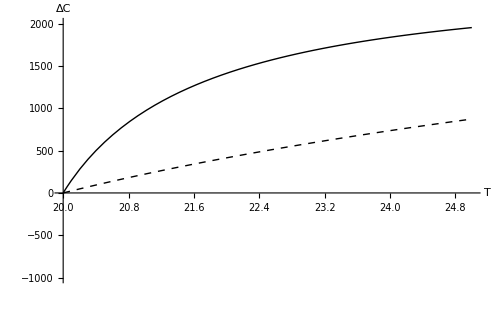

```mathematica
testparam={IS->3 10^-3,VmU0->4 10^3,EvU->46,dM->10^-6,eC->5 10^-6,γM->0.7,eD->10^-2,dZ->2 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,x0->20,c->1.075};
Plot[{ΔCtoteco/.testparam,ΔCtotecoevo/.testparam},{x,20,25},AxesOrigin->{20,0},PlotRange->{{20,25},{-1000,2000}},PlotStyle->{{Black,Dashed,Thick},{Black,Thick}},ImageSize->500,AxesLabel->{"T","ΔC"}]
```

### Supplementary Figure 10b

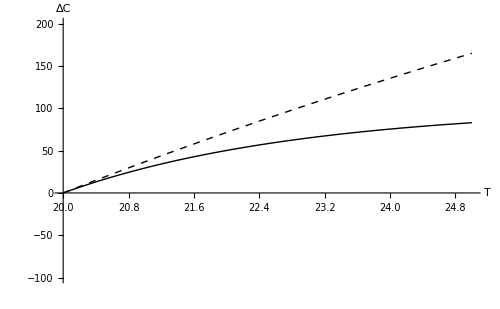

```mathematica
testparam={IS->3 10^-3,VmU0->4 10^3,EvU->46,dM->10^-6,eC->5 10^-6,γM->0.7,eD->10^-2,dZ->2 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,x0->20,c->1.12};
Plot[{ΔCtoteco/.testparam,ΔCtotecoevo/.testparam},{x,20,25},AxesOrigin->{20,0},PlotRange->{{20,25},{-100,200}},PlotStyle->{{Black,Dashed,Thick},{Black,Thick}},ImageSize->500,AxesLabel->{"T","ΔC"}]
```

### Supplementary Figure 10c

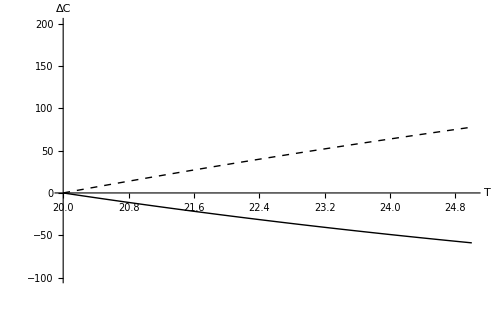

```mathematica
testparam={IS->3 10^-3,VmU0->4 10^3,EvU->46,dM->10^-6,eC->5 10^-6,γM->0.7,eD->10^-2,dZ->2 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,x0->20,c->1.35};
Plot[{ΔCtoteco/.testparam,ΔCtotecoevo/.testparam},{x,20,25},AxesOrigin->{20,0},PlotRange->{{20,25},{-100,200}},PlotStyle->{{Black,Dashed,Thick},{Black,Thick}},ImageSize->500,AxesLabel->{"T","ΔC"}]
```

## Supplementary Table 1 (Arrhenius parameter values)

### VmD

### 1) Calculate aVD CA, β-Glucosidase: Vint = 4.93, Vslope = 0.046 and if I want Allison’s 20°C-value (0.42) --> I need aVD = 1.2x10-3

```mathematica
Solve[aV Exp[Vint+Vslope x]==0.42,aV]/.x->20/.Vint->4.93/.Vslope->0.046
```

{{aV→0.00120956}}

### 2) Calculate VmD at several T to build a dataset

```mathematica
1.2 10^-3Exp[Vint+Vslope x]/.Vint->4.93/.Vslope->0.046/.x->10
```

0.263044

### 3) Fit the dataset with an Arrhenius to find V0D and EvD --> V0D = 1.15 x 10^6, EvD = 36.1

```mathematica
dataVmD={{0,0.16605541480795272},{10,0.26304406266474534},{20,0.4166812565744813},{30,0.6600539385744466},{40,1.0455742727889266},{50,1.6562670049044623}};
```

FittedModel[1.14842×10^6 ⅇ^(-4347.06/(273+x))]

1.14842×10^6 ⅇ^(-4347.06/(273+x))

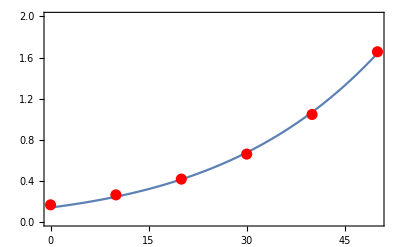

0.000330084

```mathematica
nlmVmD=NonlinearModelFit[dataVmD,VmD0 Exp[-EvD/(R(x+273))]/.R->8.314 10^-3,{VmD0,EvD},x]
Normal[nlmVmD]
Show[Plot[nlmVmD[x],{x,0,50},PlotRange->{{0,50},{0,2}}],ListPlot[dataVmD,PlotStyle->{Red,PointSize[0.02]}],Frame->True]
nlmVmD["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

```mathematica
Solve[4347.058585613794==EvD/R,EvD]/.R->8.314 10^-3
```

{{EvD→36.1414}}

#### 4) Plot

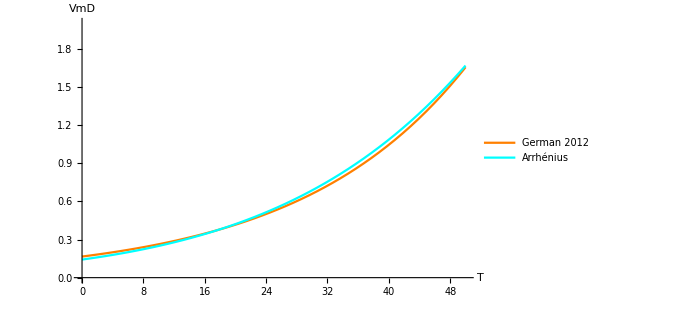

```mathematica
Plot[{1.2 10^-3Exp[Vint+Vslope x]/.Vint->4.93/.Vslope->0.046,1.15 10^6 Exp[-36.1/(R(x+273))]/.R->8.314 10^-3},{x,0,50},PlotRange->{{0,50},{0,2}},AxesLabel->{"T","VmD"},PlotStyle->{Orange,Cyan},PlotLegends->{"German 2012","Arrhénius"},ImageSize->500]
```

## Supplementary Table 2 (Sensitivity analysis)

### Temperature (x)

```mathematica
testxone={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,φ->0.1,x0->20};
LPx=4.9;
HPx=490;
LOx=SC3ecox/.x->LPx/.testxone;
HOx=SC3ecox/.x->HPx/.testxone;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

1.62621

```mathematica
LOx=DC3ecox/.x->LPx/.testxone;
HOx=DC3ecox/.x->HPx/.testxone;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

0.837385

```mathematica
LOx=M3ecox/.x->LPx/.testxone;
HOx=M3ecox/.x->HPx/.testxone;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

0.0598614

```mathematica
LOx=Z3ecox/.x->LPx/.testxone;
HOx=Z3ecox/.x->HPx/.testxone;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

0.0598614

## Supplementary Table 3 (5 biomes Arrhenius parameter values)

### VmD (Costa Rica) --> EvD = 48.9, V0D = 1.23 x 10^8

```mathematica
aV Exp[Vint+Vslope x]/.aV->1.2 10^-3/.Vint->4.11/.Vslope->0.061/.x->0
```

0.0731361

```mathematica
dataVmD={{0,0.07313606108354667},{10,0.1346019032013711},{20,0.2477255689875699},{30,0.45592191544577043},{40,0.8390930085790629},{50,1.5442931194870564}};
```

FittedModel[1.23174×10^8 ⅇ^(-5878.73/(273+x))]

1.23174×10^8 ⅇ^(-5878.73/(273+x))

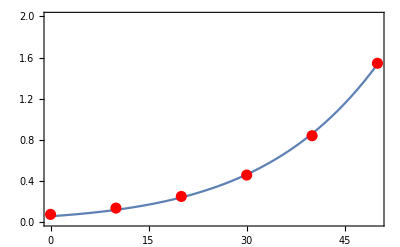

0.000202851

```mathematica
nlmVmD=NonlinearModelFit[dataVmD,VmD0 Exp[-EvD/(R(x+273))]/.R->8.314 10^-3,{VmD0,EvD},x]
Normal[nlmVmD]
Show[Plot[nlmVmD[x],{x,0,50},PlotRange->{{0,50},{0,2}}],ListPlot[dataVmD,PlotStyle->{Red,PointSize[0.02]}],Frame->True]
nlmVmD["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

```mathematica
Solve[5878.734148905386==EvD/R,EvD]/.R->8.314 10^-3
```

{{EvD→48.8758}}

### KmD (Costa Rica) --> EkD = 5.2, K0D = 5.5 x 10^3

```mathematica
aK Exp[Kint+Kslope x]/.aK->16.56/.Kint->3.32/.Kslope->0.007/.x->50
```

650.012

```mathematica
dataKmD={{0,458.0554052490373},{10,491.268169597308},{20,526.8891310828969},{30,565.092903700332},{40,606.0667623873072},{50,650.0115610466424}};
```

FittedModel[4442.78 ⅇ^(-622.9/(273+x))]

4442.78 ⅇ^(-622.9/(273+x))

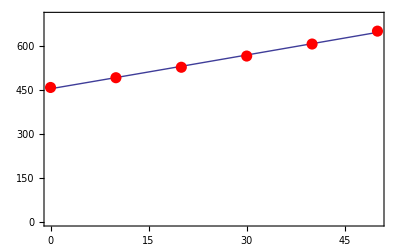

10.2315

```mathematica
nlmKmD=NonlinearModelFit[dataKmD,KmD0 Exp[-EkD/(R(x+273))]/.R->8.314 10^-3,{KmD0,EkD},x]
Normal[nlmKmD]
Show[Plot[nlmKmD[x],{x,0,50},PlotRange->{{0,50},{0,700}}],ListPlot[dataKmD,PlotStyle->{Red,PointSize[0.02]}],Frame->True]
nlmKmD["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

```mathematica
Solve[622.9003784602833==EkD/R,EkD]/.R->8.314 10^-3
```

{{EkD→5.17879}}